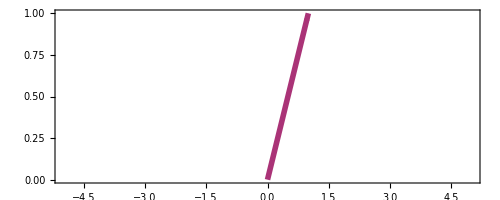

```mathematica
ClearAll[a];tk=0.01;ak=tk*6;
a[x_,y_,dx_,dy_,col_]:={Thickness[tk],Arrowheads[ak],col,Arrow[{{x,y},{x+dx,y+dy}}]};
Graphics[a[0,0,1,1,redpurple],PlotRange->{{-5,5},All},Frame->True]
```

```mathematica
xl=-0.2;ay=0.3;yl=0.5;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,-yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
1;anim=Animate[Graphics[{Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/vectorfluxanimation.mp4",anim,"AnimationDuration"->10];
Export["media/vectorfluxanimation.webp",anim,"AnimationDuration"->10];
Export["media/vectorfluxanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
xl=0.5;ay=0.5;yl=0;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
he=1;anim=Animate[Graphics[{Text[Style["momentum-flux: pressure",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["momentum-flux: pressure",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/pressureanimation.mp4",anim,"AnimationDuration"->10];
Export["media/pressureanimation.webp",anim,"AnimationDuration"->10];
Export["media/pressureanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
xl=-0.5;ay=0.5;yl=0;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
he=1;anim=Animate[Graphics[{tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["momentum-flux: tension",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/tensionanimation.mp4",anim,"AnimationDuration"->10];
Export["media/tensionanimation.webp",anim,"AnimationDuration"->10];
Export["media/tensionanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
xl=0;ay=0.3;yl=0.5;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,-yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
1;anim=Animate[Graphics[{Text[Style["momentum-flow: shear force",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["momentum-flux: shear force",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/shearforceanimation.mp4",anim,"AnimationDuration"->10];
Export["media/shearforceanimation.webp",anim,"AnimationDuration"->10];
Export["media/shearforceanimation.gif",anim,"AnimationDuration"->10];
```